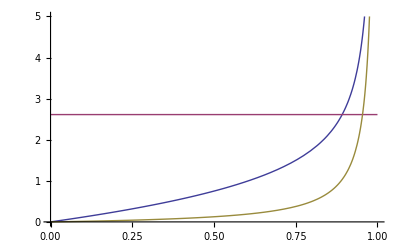

```mathematica
Lambda=0.5;V=1;Plot[{PolyLog[3/2,z]+Lambda^3*z/(1-z)/V,2.612,Lambda^3*z/(1-z)/V},{z,0,1},PlotRange->{0,5}]
```

```mathematica
NIntegrate[1/(Exp[x]-1),{x,1,Infinity}]
```

0.458675

```mathematica
Series[Exp[x]-1,{x,0,10}]
```

x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Series[Sqrt[x],{x,0,10}]
```

√x+O[x]^(21/2)

```mathematica
Sqrt
```

```mathematica
Integrate[1/x^(0.9999),{x,0,1}]
```

10000.

Power::infy: Infinite expression 1/0. encountered.

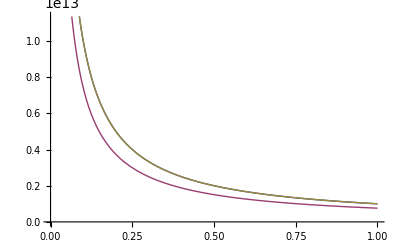

```mathematica
Plot[{1/x,x^-.99,1/(Exp[x]-1)},{x,0,0.000000000001}]
```

```mathematica
Solve[b==x+Log[x],x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ProductLog[ⅇ^b]}}

```mathematica
Series[ProductLog[b],{b,0,10}]
```

b-b^2+(3 b^3)/2-(8 b^4)/3+(125 b^5)/24-(54 b^6)/5+(16807 b^7)/720-(16384 b^8)/315+(531441 b^9)/4480-(156250 b^10)/567+O[b]^11

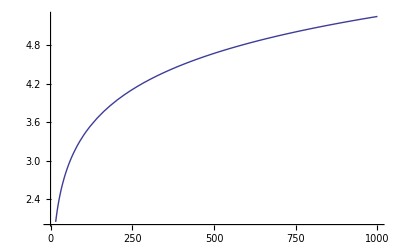

```mathematica
Plot[ProductLog[x],{x,0,1000}]
```

```mathematica
D[Sinh[x],x]
```

Cosh[x]

```mathematica
D[k T Log[2 Sinh[h w/k/T/2]],T]
```

-(h w Coth[(h w)/(2 k T)])/(2 T)+k Log[2 Sinh[(h w)/(2 k T)]]

```mathematica
D[1/Tanh[x],x]
```

-Csch[x]^2

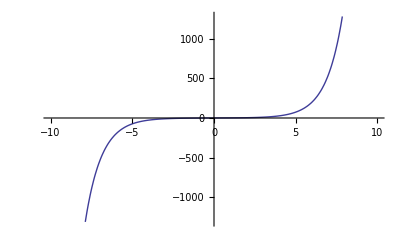

```mathematica
Plot[1/Csch[x],{x,-10,10}]
```

```mathematica
D[h w/2/Tanh[h w /k/T/2],T]
```

(h^2 w^2 Csch[(h w)/(2 k T)]^2)/(4 k T^2)

```mathematica
t:=c/(n+1/2);
```

```mathematica
k T Log[e/k/T]-T D[k T Log[e/k/T],T]
```

k T Log[e/(k T)]-T (-k+k Log[e/(k T)])

```mathematica
Simplify[%]
```

k T

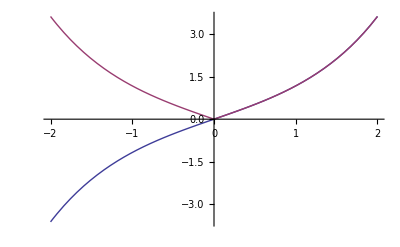

```mathematica
Plot[{Sinh[x],1/Sqrt[1/Tanh[x]^2-1]},{x,-2,2}]
```

```mathematica
Solve[Sqrt[x^2+1]/x==n,x]
```

{{x→-1/(√(-1+n^2))},{x→1/(√(-1+n^2))}}

```mathematica
D[1/(√(-1+n^2)),n]
```

-n/((-1+n^2)^(3/2))

```mathematica
D[Sqrt[x^2+1]/x,x]
```

1/(√(1+x^2))-(√(1+x^2))/x^2

```mathematica
D[6 e/( Exp[2 e /k/T]+3),T]
```

(12 e^2 ⅇ^((2 e)/(k T)))/((3+ⅇ^((2 e)/(k T)))^2 k T^2)

```mathematica
x/(3+x)^2
```

x/(3+x)^2

```mathematica
Factor[%]
```

x/(3+x)^2

```mathematica
Sum[1/2^n,{n,1,Infinity}]
```

1

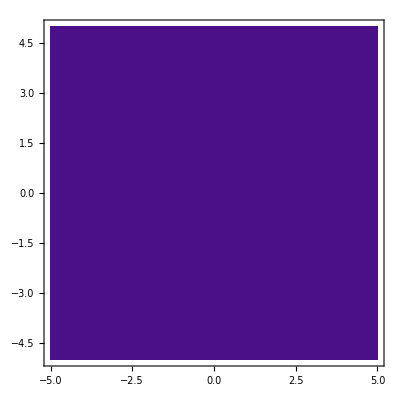

```mathematica
a=1;b=0;DensityPlot[f[a*x+b*y-1,0.01],{x,-5,5},{y,-5,5}]
```

```mathematica
f[x_,e_]:=UnitStep[x+e/2]-UnitStep[x-e/2];
```

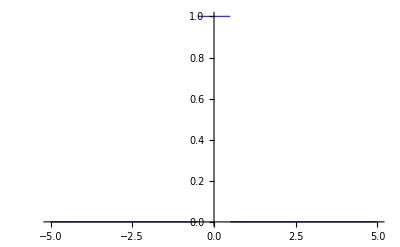

```mathematica
Plot[f[x,1],{x,-5,5}]
```